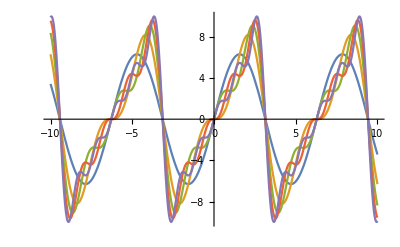

```mathematica
(***********esercizio 1*************)

f[x_]:=x;

a[n_]:=Integrate[f[x] Cos[n x],{x,-Pi,Pi}];
b[n_]:=Integrate[f[x] Sin[n x],{x,-Pi,Pi}];

g[x_,k_]:=a[0]/2+Sum[a[n] Cos[n x]+b[n] Sin[n x],{n,1,k}];

gra1=Plot[Evaluate[Table[g[x,k],{k,1,5}]],{x,-10,10}]
```

```mathematica
(***********esercizio 2*************)
V[x_,mu_,lambda_]:=-mu x^2+lambda x^4;

gra2=Plot[V[x,4,1],{x,-3,3}];

Vp[x_]=D[V[x,mu,lambda],x];

minmax=Solve[Vp[x]==0,x];

valminmax=V[x,mu,lambda]/.minmax;

gra3=ParametricPlot3D[w=V[r,4,1];{r Sin[phi],r Cos[phi],w},{r,0,2},{phi,0,2 Pi}];
```

```mathematica
(************esercizio 3***************)

s[n_]:=Normal[Series[ArcSinh[x],{x,0,n}]];

funs=Join[Table[s[i],{i,{5,9,11}}],{ArcSinh[x]}];

gra4=Plot[funs,{x,-5,5},PlotRange->{-3,3}];
```